```mathematica
Quiet@Remove["Global`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
1+1
```

2

```mathematica
a=5
```

5

```mathematica
b=3;
```

```mathematica
a
```

5

```mathematica
?a
```

Global`a

a=5

```mathematica
a+b
```

8

```mathematica
(*place for comments*)
(*Wolfam is case sensitive*)
```

```mathematica
Sin[Pi]
```

0

```mathematica
(*sin(π) Sin[π]*)
```

```mathematica
Sin[Pi]
```

0

```mathematica
Sin[5]
```

Sin[5]

```mathematica
Sin[5.]
```

-0.958924

```mathematica
(*ctrl+2*)
√2
```

√2

```mathematica
√2.
```

1.41421

```mathematica
c=Sin[5];
N[c]
```

-0.958924

```mathematica
N[c,200]
```

-0.95892427466313846889315440615599397335246154396460177813167245423510255808655960307699595542953286659653063846166337893719140170112056579017229647453110171092058800456089439785783766016074199381863943

```mathematica
Solve[4 x+y==7&&2 x-y==1,{x,y}]
```

{{x→4/3,y→5/3}}

```mathematica
&&
```

```mathematica
list1={1,2,3,5}
```

{1,2,3,5}

```mathematica
list2={{1,2},{3,4}}
MatrixForm[list2]
```

{{1,2},{3,4}}

(1 | 2
3 | 4)

```mathematica
Solve[{4 x+y==7,2 x-y==1},{x,y}]
```

{{x→4/3,y→5/3}}

```mathematica
Equal[4x+y,7]
```

4 x+y==7

```mathematica
FullForm[4 x+y==7]
```

Equal[Plus[Times[4,x],y],7]

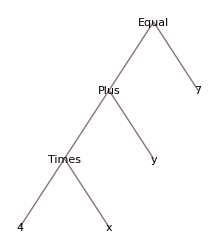

```mathematica
TreeForm[4 x+y==7]
```

```mathematica
?Equal
```

lhs==rhs returns True if lhs and rhs are identical.

```mathematica
Solve[{4 x+y==7,2 x-y==1},{x,y}]
```

{{x→4/3,y→5/3}}

```mathematica
Equal[4x+y,7]
```

4 x+y==7

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[{…,w[f_i],…},…] plots f_i with features defined by the symbolic wrapper w.
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.

```mathematica
Plot[Sin[x],{x,0,6Pi},PlotStyle->{Red,Dashed},AspectRatio->1];
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,6Pi},PlotStyle->{{Red,Dashed},Blue}];
```

```mathematica
num={1,2,3,10}
```

{1,2,3,10}

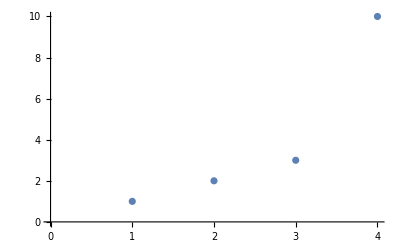

```mathematica
ListPlot[num]
```

```mathematica
data=Table[{i,Sin[i^2]},{i,0,10.,.1}];
```

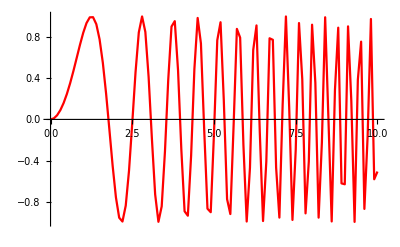

```mathematica
ListLinePlot[data,PlotStyle->Red]
```

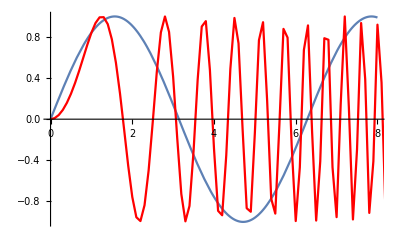

```mathematica
Show[Plot[Sin[x],{x,0,8}],ListLinePlot[data,PlotStyle->Red]]
```

```mathematica
FullForm[ListLinePlot[data,PlotStyle->Red]]
```

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

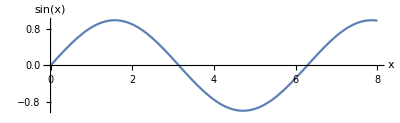

```mathematica
Plot[Sin[x],{x,0,8},AspectRatio->(.5)/GoldenRatio,AxesLabel->{"x","sin(x)"}]
```

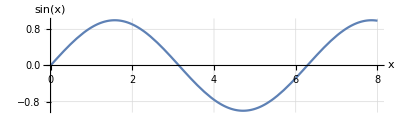

```mathematica
Plot[Sin[x],{x,0,8},AspectRatio->(.5)/GoldenRatio,AxesLabel->{"x","sin(x)"},GridLines->Automatic]
```

```mathematica
a
```

5

```mathematica
kyncl is a stupid guy
```

5 guy is kyncl stupid

```mathematica
kyncl*is*a*stupid*guy
```

5 guy is kyncl stupid

sin x

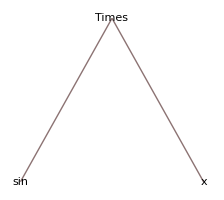

```mathematica
sin(x)
TreeForm[%]
```

```mathematica
myFirstPlot=Plot[Sin[x],{x,0,8},AspectRatio->(.5)/GoldenRatio,AxesLabel->{"x","sin(x)"},GridLines->Automatic]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\H3\Desktop\MAA

```mathematica
FileNames[]
```

{seminar_08_04.nb}

```mathematica
Export["myPlot.png",myFirstPlot]
```

myPlot.png

```mathematica
Export["myPlot.png",myFirstPlot,ImageResolution->300]
```

myPlot.png

```mathematica
(*homework*)
(*DSolve*)
DSolve
NDSolve
FindRoot
(*play in the help*)
```